```mathematica
x=RandomVariate[PoissonDistribution[RandomReal[{10,500}]],10*10]
```

{205,207,239,183,201,204,198,208,191,186,192,178,214,184,197,195,204,215,207,201,209,200,201,215,196,182,198,187,177,212,210,206,177,189,177,219,206,202,194,213,195,189,207,185,206,222,195,180,212,192,194,195,176,206,189,184,186,216,186,216,205,192,191,216,201,175,210,204,203,200,214,201,186,189,165,173,207,214,191,221,200,213,195,205,218,195,207,183,216,212,217,185,202,182,193,212,181,222,208,206}

```mathematica
x=RandomInteger[{0,100},10*10]
```

{20,2,31,84,14,55,40,86,45,37,67,49,84,65,79,0,85,10,65,85,35,49,8,60,82,9,25,13,53,82,91,75,93,13,46,71,3,43,92,26,77,20,16,28,31,22,63,62,38,44,42,46,59,38,34,40,59,12,10,45,61,68,19,83,69,2,42,72,34,56,71,56,34,13,9,37,29,58,40,53,61,59,53,35,94,24,16,91,82,14,82,34,93,37,63,62,19,27,76,76}

```mathematica
s=Join[
ArrayReshape[Range@Length@x,{10,10}],
Transpose[ArrayReshape[Range@Length@x,{10,10}]][[{3,6}]],
{Range@Length@x}
]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100},{3,13,23,33,43,53,63,73,83,93},{6,16,26,36,46,56,66,76,86,96},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}}

```mathematica
s=Join[
ArrayReshape[Range@Length@x,{10,10}],
Transpose@ArrayReshape[Range@Length@x,{10,10}],
RandomChoice[Range@Length@x,{100,5}],
{Range@Length@x}
];
```

```mathematica
y=RandomVariate@PoissonDistribution[Total[x[[#]]]]&/@s
```

{400,583,429,587,413,350,535,406,516,569,592,471,492,465,521,332,373,435,546,550,315,281,313,208,211,105,327,199,267,221,260,310,245,176,313,316,384,140,217,280,276,233,203,212,168,250,252,356,333,206,219,277,212,164,210,212,332,251,231,297,336,179,271,176,320,266,279,191,200,201,226,248,238,184,280,245,283,187,185,280,418,150,262,81,271,265,285,116,275,227,187,224,207,226,213,294,196,168,235,258,96,255,105,264,219,185,285,281,153,274,211,247,219,144,197,265,290,140,146,324,4903}

```mathematica
λ=100.;
```

```mathematica
elem=3;
```

```mathematica
Select[s,MemberQ[elem]]
```

{{1,2,3,4,5,6,7,8,9,10},{3,13,23,33,43,53,63,73,83,93}}

```mathematica
PDF[PoissonDistribution[λ],xp]*PDF[]
```

Piecewise[{{(ⅇ^-λ λ^n)/(n!), n≥0}, {0, True}}]

Gaussian version:

```mathematica
a=Boole@Outer[MemberQ,s,Range@Length@x,1];
```

```mathematica
Dimensions[x]
```

{100}

```mathematica
Dimensions[y]
```

{12}

```mathematica
Dimensions[a]
```

{12,100}

```mathematica
mu0=ConstantArray[100,Length@x];
sigma0=100*IdentityMatrix@Length@x;
ySigma=5;
```

```mathematica
sigma=Inverse[Inverse[sigma0]+(1/ySigma^2) Transpose[a].a];
mu=sigma.(Inverse[sigma0].mu0+(1/ySigma^2) Transpose[a].y);
```

```mathematica
N@mu
```

{21.5409,-10.48,39.7346,46.3724,42.8944,63.2506,46.3888,101.38,14.617,49.5726,53.1327,85.5171,75.7579,86.0004,85.668,-1.84958,69.0524,13.1952,79.6504,50.0827,42.7893,54.0512,11.1982,66.3745,68.9865,29.8162,42.7624,-6.055,48.4746,87.147,114.656,64.8594,101.767,26.9589,40.8323,75.2796,-5.30695,24.3229,110.411,39.5274,90.7891,34.2267,12.8608,30.2518,34.2118,16.9808,48.9376,66.7533,43.6139,41.9911,47.7101,31.5986,51.5913,20.3539,45.0818,9.93117,73.173,19.6544,5.5241,39.6369,63.3973,69.2582,31.7169,85.1382,55.348,13.1759,55.3447,87.1404,22.7277,65.0574,67.4736,51.9903,36.0316,19.3741,21.5585,64.592,29.1253,25.5243,38.3234,59.8302,34.2154,69.7814,61.9352,36.041,58.4871,31.1228,28.1981,91.8906,81.5933,40.7772,78.0794,24.96,83.3394,59.4435,78.8056,48.5685,-2.74306,28.5434,98.1254,83.752}

```mathematica
x
```

{20,2,31,84,14,55,40,86,45,37,67,49,84,65,79,0,85,10,65,85,35,49,8,60,82,9,25,13,53,82,91,75,93,13,46,71,3,43,92,26,77,20,16,28,31,22,63,62,38,44,42,46,59,38,34,40,59,12,10,45,61,68,19,83,69,2,42,72,34,56,71,56,34,13,9,37,29,58,40,53,61,59,53,35,94,24,16,91,82,14,82,34,93,37,63,62,19,27,76,76}

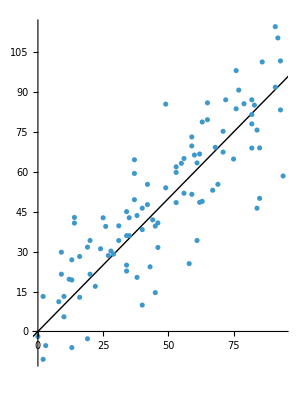

```mathematica
ListPlot[Transpose@{x,mu},AspectRatio->Automatic,Epilog->InfiniteLine[{0,0},{1,1}]]
```